# Prática 1: Estatística de Contagem com um Contador Geiger-Mueller

## Análise de dados

## Importando os dados

```mathematica
SetDirectory["C:\\Users\\laris\\OneDrive\\Documentos\\LAB4"];
```

```mathematica
dados50G2cru = Import["G2_50ms.txt", "Data"];
```

```mathematica
dados100G2cru = Import["G2_100ms.txt", "Data"];
```

```mathematica
dados200G2cru = Import["G2_200ms.txt", "Data"];
```

```mathematica
dados500G2cru = Import["G2_500ms.txt", "Data"];
```

```mathematica
dados1000G2cru = Import["G2_1000ms.txt", "Data"];
```

```mathematica
dados2000G2cru = Import["G2_2000ms.txt", "Data"];
```

```mathematica
dados5000G2cru = Import["G2_5000ms.txt", "Data"];
```

```mathematica
dadosBGG2cru = Import["G2_BG1000ms.txt", "Data"];
```

### Organizando os arquivos

```mathematica
n50G2 = Length[dados50G2cru];
dados50G2=ToExpression[Table[StringDrop[dados50G2cru[[i,3]],3],{i,n50G2}]];
```

```mathematica
n100G2 = Length[dados100G2cru];
dados100G2=ToExpression[Table[StringDrop[dados100G2cru[[i,3]],3],{i,n100G2}]];
```

```mathematica
n200G2 = Length[dados200G2cru];
dados200G2=ToExpression[Table[StringDrop[dados200G2cru[[i,3]],3],{i,n200G2}]];
```

```mathematica
n500G2 = Length[dados500G2cru];
dados500G2=ToExpression[Table[StringDrop[dados500G2cru[[i,3]],3],{i,n500G2}]];
```

```mathematica
n1000G2 = Length[dados1000G2cru];
dados1000G2=ToExpression[Table[StringDrop[dados1000G2cru[[i,3]],3],{i,n1000G2}]];
```

```mathematica
n2000G2 = Length[dados2000G2cru];
dados2000G2=ToExpression[Table[StringDrop[dados2000G2cru[[i,3]],3],{i,n2000G2}]];
```

```mathematica
n5000G2 = Length[dados5000G2cru];
dados5000G2=ToExpression[Table[StringDrop[dados5000G2cru[[i,3]],3],{i,n5000G2}]];
```

1. Uma tabela mostrando os valores da media experimental (com sua incerteza) e da variância da amostra para cada intervalo de tempo (t)

Calculando a média experimental de todos os conjuntos de dados

```mathematica
med50G2 = N[Total[dados50G2] / n50G2]; (*Ou utilizando a função Mean*)
```

```mathematica
med100G2 = N[Total[dados100G2] / n100G2];
```

```mathematica
med200G2 = N[Total[dados200G2] / n200G2];
```

```mathematica
med500G2 = N[Total[dados500G2] / n500G2];
```

```mathematica
med1000G2 = N[Total[dados1000G2] / n1000G2];
```

```mathematica
med2000G2 = N[Total[dados2000G2] / n2000G2];
```

```mathematica
med5000G2 = N[Total[dados5000G2] / n5000G2];
```

Calculando a variância de todos os conjuntos de dados

```mathematica
var50G2 = N[Total[(dados50G2 - med50G2)^2/(n50G2 - 1)]];(*Também podemos usar N[Variance[dados50G2]]*)
```

```mathematica
var100G2 = N[Total[(dados100G2 - med100G2)^2/(n100G2 - 1)]];
```

```mathematica
var200G2 = N[Total[(dados200G2 - med200G2)^2/(n200G2 - 1)]];
```

```mathematica
var500G2 = N[Total[(dados500G2 - med500G2)^2/(n500G2 - 1)]];
```

```mathematica
var1000G2 = N[Total[(dados1000G2 - med1000G2)^2/(n1000G2 - 1)]];
```

```mathematica
var2000G2 = N[Total[(dados2000G2 - med2000G2)^2/(n2000G2 - 1)]];
```

```mathematica
var5000G2 = N[Total[(dados5000G2 - med5000G2)^2/(n5000G2 - 1)]];
```

Obtendo a incerteza de cada média amostral

```mathematica
(*Calculando o desvio padrão para diferentes intervalos de tempo*)
desvioPadrao50G2=Sqrt[var50G2];
desvioPadrao100G2=Sqrt[var100G2];
desvioPadrao200G2=Sqrt[var200G2];
desvioPadrao500G2=Sqrt[var500G2];
desvioPadrao1000G2=Sqrt[var1000G2];
desvioPadrao2000G2=Sqrt[var2000G2];
desvioPadrao5000G2=Sqrt[var5000G2];

(*Calculando a incerteza da média para diferentes intervalos de tempo*)
incerteza50G2=desvioPadrao50G2/Sqrt[n50G2];
incerteza100G2=desvioPadrao100G2/Sqrt[n100G2];
incerteza200G2=desvioPadrao200G2/Sqrt[n200G2];
incerteza500G2=desvioPadrao500G2/Sqrt[n500G2];
incerteza1000G2=desvioPadrao1000G2/Sqrt[n1000G2];
incerteza2000G2=desvioPadrao2000G2/Sqrt[n2000G2];
incerteza5000G2=desvioPadrao5000G2/Sqrt[n5000G2];
```

Formando uma tabela com os dados

```mathematica
(*Definindo os dados*)dados={{"Intervalo de Tempo","Média","Incerteza da média amostral","Variância"},{"50 ms",med50G2,incerteza50G2, var50G2},{"100 ms",med100G2,incerteza100G2, var100G2},{"200 ms",med200G2,incerteza200G2,var200G2},{"500 ms",med500G2,incerteza500G2,var500G2},{"1000 ms",med1000G2,incerteza1000G2, var1000G2},{"2000 ms",med2000G2,incerteza2000G2,var2000G2},{"5000 ms",med5000G2,incerteza5000G2, var5000G2}};

(*Criando a tabela usando TableForm*)
TableForm[dados,TableHeadings->{None,None}];

(*Ou usando Grid*)
Grid[dados,Frame->All]
```

Intervalo de Tempo | Média | Incerteza da média amostral | Variância
50 ms | 0.675824 | 0.0598182 | 0.651236
100 ms | 1.34906 | 0.0830015 | 1.46052
200 ms | 2.67172 | 0.114979 | 2.61757
500 ms | 6.53535 | 0.180956 | 6.48352
1000 ms | 13.5179 | 0.257722 | 12.952
2000 ms | 26.5165 | 0.377621 | 25.9528
5000 ms | 65.5297 | 0.527046 | 56.1111

Observação : é necessário adequar o número de algarismos significativos da incerteza e da medida ao passar para o relatório

2. para cada valor de t, um histograma com os dados experimentais superposto às curvas Gaussiana e Poissoniana ajustadas aqueles dados;

Definição de uma função Poissoniana

```mathematica
p50G2[x_]:= n50G2*med50G2^x*Exp[-med50G2]/x!
```

```mathematica
p100G2[x_]:= n100G2*med100G2^x*Exp[-med100G2]/x!
```

```mathematica
p200G2[x_]:= n200G2*med200G2^x*Exp[-med200G2]/x!
```

```mathematica
p500G2[x_]:= n500G2*med500G2^x*Exp[-med500G2]/x!
```

```mathematica
p1000G2[x_]:=If[x==0,0,n1000G2*med1000G2^x*Exp[-med1000G2]/x!]
```

```mathematica
p2000G2[x_]:= n2000G2*med2000G2^x*Exp[-med2000G2]/x!
```

```mathematica
p5000G2[x_]:= n5000G2*med5000G2^x*Exp[-med5000G2]/x!
```

Definição de uma função Gaussiana

```mathematica
g50G2[x_] := n50G2*Exp[-(x-med50G2)^2/(2*med50G2)]/Sqrt[2*Pi*med50G2]
```

```mathematica
g100G2[x_] := n100G2*Exp[-(x-med100G2)^2/(2*med100G2)]/Sqrt[2*Pi*med100G2]
```

```mathematica
g200G2[x_] := n200G2*Exp[-(x-med200G2)^2/(2*med200G2)]/Sqrt[2*Pi*med200G2]
```

```mathematica
g500G2[x_] := n500G2*Exp[-(x-med500G2)^2/(2*med500G2)]/Sqrt[2*Pi*med500G2]
```

```mathematica
g1000G2[x_] := n1000G2*Exp[-(x-med1000G2)^2/(2*med1000G2)]/Sqrt[2*Pi*med1000G2]
```

```mathematica
g2000G2[x_] := n2000G2*Exp[-(x-med2000G2)^2/(2*med2000G2)]/Sqrt[2*Pi*med2000G2]
```

```mathematica
g5000G2[x_] := n5000G2*Exp[-(x-med5000G2)^2/(2*med5000G2)]/Sqrt[2*Pi*med5000G2]
```

Definição do histograma para cada intervalo

```mathematica
hist50G2=Histogram[dados50G2];
```

```mathematica
hist100G2=Histogram[dados100G2];
```

```mathematica
hist200G2=Histogram[dados200G2];
```

```mathematica
hist500G2=Histogram[dados500G2];
```

```mathematica
hist1000G2=Histogram[dados1000G2];
```

```mathematica
hist2000G2=Histogram[dados2000G2];
```

```mathematica
hist5000G2=Histogram[dados5000G2];
```

Definição da curva de Poisson para cada intervalo

```mathematica
grafPoiN50G2 = Plot[n50G2 * med50G2^x*Exp[-med50G2]/x!, {x,0, Max[dados50G2]}, PlotLegends->{"Poisson"}];
```

```mathematica
grafPoiN100G2 = Plot[n100G2 * med100G2^x*Exp[-med100G2]/x!, {x,0, Max[dados100G2]}, PlotLegends->{"Poisson"}];
```

```mathematica
grafPoiN200G2 = Plot[n200G2 * med200G2^x*Exp[-med200G2]/x!, {x,0, Max[dados200G2]}, PlotLegends->{"Poisson"}];
```

```mathematica
grafPoiN500G2 = Plot[n500G2 * med500G2^x*Exp[-med500G2]/x!, {x,0, Max[dados500G2]}, PlotLegends->{"Poisson"}];
```

```mathematica
grafPoiN1000G2 = Plot[n1000G2 * med1000G2^x*Exp[-med1000G2]/x!, {x,5, Max[dados1000G2]}, PlotLegends->{"Poisson"}];
```

```mathematica
grafPoiN2000G2 = Plot[n2000G2 * med2000G2^x*Exp[-med2000G2]/x!, {x,13, Max[dados2000G2]}, PlotLegends->{"Poisson"}];
```

```mathematica
grafPoiN5000G2 = Plot[n5000G2 * med5000G2^x*Exp[-med5000G2]/x!, {x,47, Max[dados5000G2]}, PlotLegends->{"Poisson"}];
```

Definição da curva de Gauss para cada intervalo

```mathematica
grafGauN50G2=Plot[n50G2*Exp[-((x-med50G2)^2/(2*var50G2))]/(Sqrt[2*Pi]*Sqrt[var50G2]),{x,0,Max[dados50G2]},PlotStyle->Red,PlotLegends->{"Gauss"}];
```

```mathematica
grafGauN100G2=Plot[n100G2*Exp[-((x-med100G2)^2/(2*var100G2))]/(Sqrt[2*Pi]*Sqrt[var100G2]),{x,0,Max[dados100G2]},PlotStyle->Red,PlotLegends->{"Gauss"}];
```

```mathematica
grafGauN200G2=Plot[n200G2*Exp[-((x-med200G2)^2/(2*var200G2))]/(Sqrt[2*Pi]*Sqrt[var200G2]),{x,0,Max[dados200G2]},PlotStyle->Red,PlotLegends->{"Gauss"}];
```

```mathematica
grafGauN500G2=Plot[n500G2*Exp[-((x-med500G2)^2/(2*var500G2))]/(Sqrt[2*Pi]*Sqrt[var500G2]),{x,0,Max[dados500G2]},PlotStyle->Red,PlotLegends->{"Gauss"}];
```

```mathematica
grafGauN1000G2=Plot[n1000G2*Exp[-((x-med1000G2)^2/(2*var1000G2))]/(Sqrt[2*Pi]*Sqrt[var1000G2]),{x,5,Max[dados1000G2]},PlotStyle->Red,PlotLegends->{"Gauss"}];
```

```mathematica
grafGauN2000G2=Plot[n2000G2*Exp[-((x-med2000G2)^2/(2*var2000G2))]/(Sqrt[2*Pi]*Sqrt[var2000G2]),{x,13,Max[dados2000G2]},PlotStyle->Red,PlotLegends->{"Gauss"}];
```

```mathematica
grafGauN5000G2=Plot[n5000G2*Exp[-((x-med5000G2)^2/(2*var5000G2))]/(Sqrt[2*Pi]*Sqrt[var5000G2]),{x,47,Max[dados5000G2]},PlotStyle->Red,PlotLegends->{"Gauss"}];
```

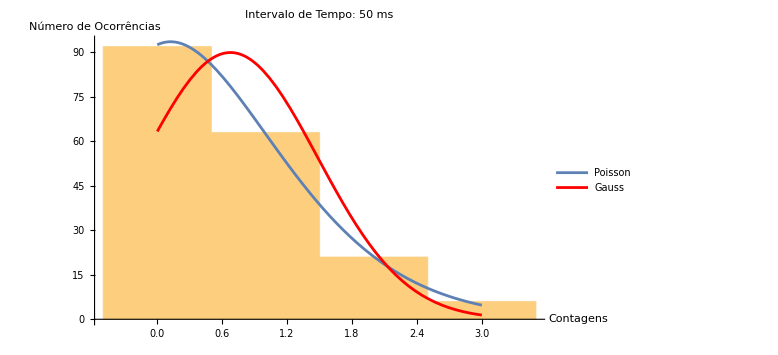
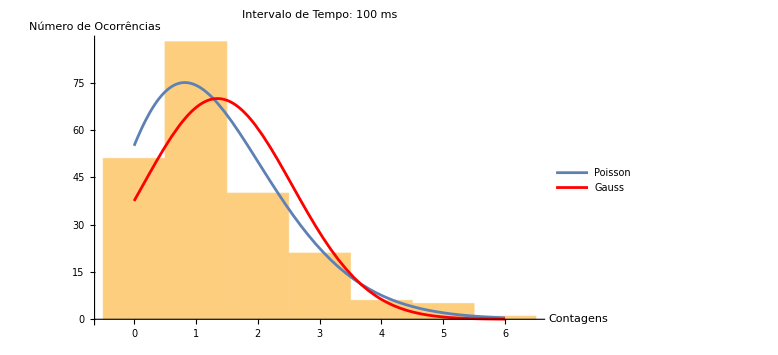
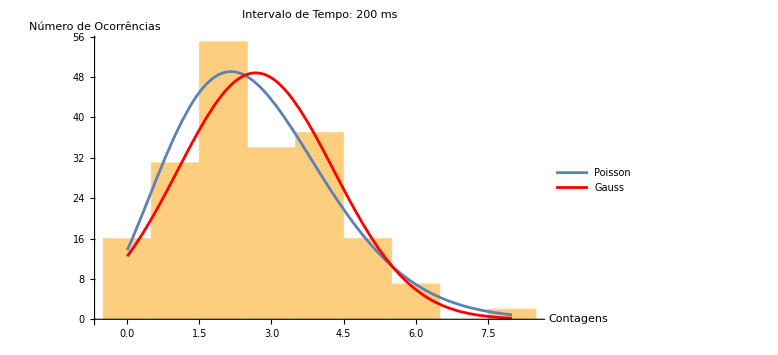
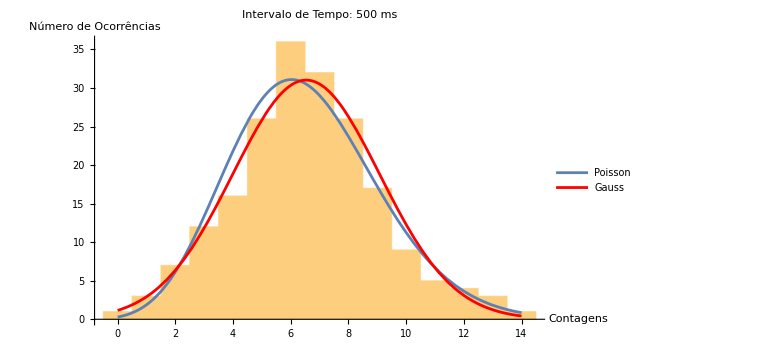
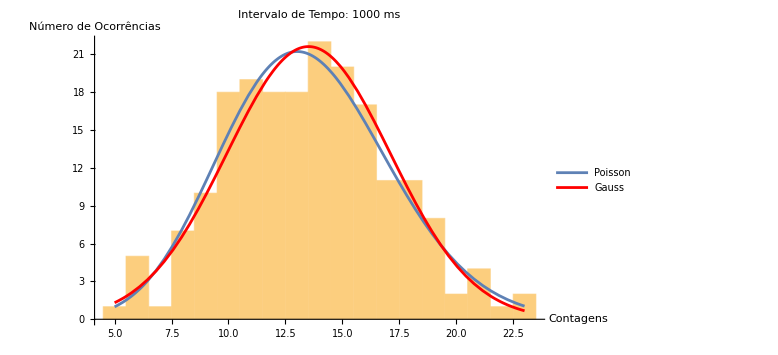
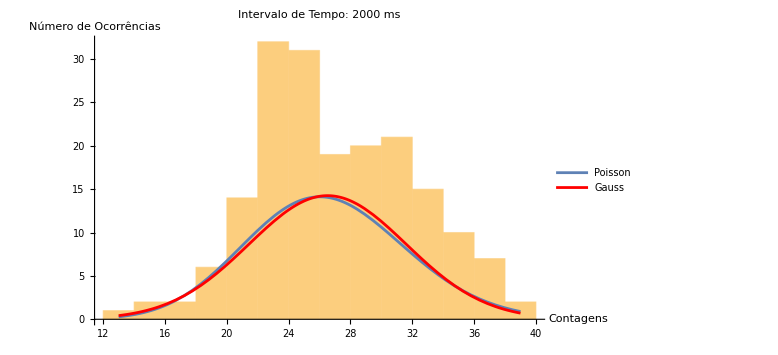
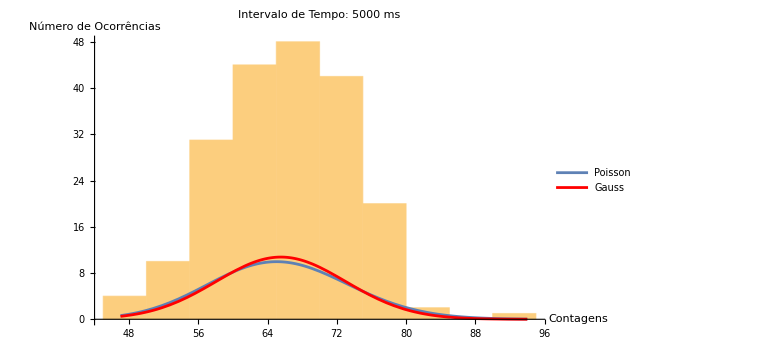
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Grid[{{Show[Histogram[dados50G2,AxesLabel->{"Contagens","Número de Ocorrências"},ImageSize->Large],grafPoiN50G2,grafGauN50G2,PlotRange->All,PlotLabel->"Intervalo de Tempo: 50 ms"],Show[Histogram[dados100G2,AxesLabel->{"Contagens","Número de Ocorrências"},ImageSize->Large],grafPoiN100G2,grafGauN100G2,PlotRange->All,PlotLabel->"Intervalo de Tempo: 100 ms"],Show[Histogram[dados200G2,AxesLabel->{"Contagens","Número de Ocorrências"},ImageSize->Large],grafPoiN200G2,grafGauN200G2,PlotRange->All,PlotLabel->"Intervalo de Tempo: 200 ms"],Show[Histogram[dados500G2,AxesLabel->{"Contagens","Número de Ocorrências"},ImageSize->Large],grafPoiN500G2,grafGauN500G2,PlotRange->All,PlotLabel->"Intervalo de Tempo: 500 ms"]},{Show[Histogram[dados1000G2,AxesLabel->{"Contagens","Número de Ocorrências"},ImageSize->Large],grafPoiN1000G2,grafGauN1000G2,PlotRange->All,PlotLabel->"Intervalo de Tempo: 1000 ms"],Show[Histogram[dados2000G2,AxesLabel->{"Contagens","Número de Ocorrências"},ImageSize->Large],grafPoiN2000G2,grafGauN2000G2,PlotRange->All,PlotLabel->"Intervalo de Tempo: 2000 ms"],Show[Histogram[dados5000G2,AxesLabel->{"Contagens","Número de Ocorrências"},ImageSize->Large],grafPoiN5000G2,grafGauN5000G2,PlotRange->All,PlotLabel->"Intervalo de Tempo: 5000 ms"]}},Spacings->{10,10}]
```

3. Uma tabela com os valores do qui-quadrado e da probabilidade (medida da qualidade do ajuste) de ambas as funções (Gaussiana e Poisson) para cada valor de t;

Definição do qui-quadrado para Poisson

```mathematica
altHist50G2 = BinCounts[dados50G2, {Min[dados50G2], Max[dados50G2]+1}];
chiquadP50G2 = N[Total[Table[(altHist50G2[[i+1]]- p50G2[i])^2/altHist50G2[[i+1]], {i, Min[dados50G2], Max[dados50G2]}]]];
```

```mathematica
altHist100G2 = BinCounts[dados100G2, {Min[dados100G2], Max[dados100G2]+1}];
chiquadP100G2 = N[Total[Table[(altHist100G2[[i+1]]- p100G2[i])^2/altHist100G2[[i+1]], {i, Min[dados100G2], Max[dados100G2]}]]];
```

```mathematica
altHist200G2=BinCounts[dados200G2,{Min[dados200G2],Max[dados200G2]+1}];
chiquadP200G2=N[Total@Table[If[altHist200G2[[i+1]]!=0,(altHist200G2[[i+1]]-p200G2[i])^2/altHist200G2[[i+1]],0],{i,Min[dados200G2],Max[dados200G2]}]];
```

```mathematica
altHist500G2 = BinCounts[dados500G2, {Min[dados500G2], Max[dados500G2]+1}];
chiquadP500G2 = N[Total[Table[(altHist500G2[[i+1]]- p500G2[i])^2/altHist500G2[[i+1]], {i, Min[dados500G2], Max[dados500G2]}]]];
```

```mathematica
altHist1000G2 = BinCounts[dados1000G2, {Min[dados1000G2], Max[dados1000G2]+1}];
chiquadP1000G2 = N[Total[Table[(altHist1000G2[[i+1 - Min[dados1000G2]]]- p1000G2[i])^2/altHist1000G2[[i+1 - Min[dados1000G2]]], {i, Min[dados1000G2], Max[dados1000G2]}]]];
```

```mathematica
altHist2000G2 = BinCounts[dados2000G2, {Min[dados2000G2], Max[dados2000G2]+1}];
chiquadP2000G2 = N[Total[Table[(altHist2000G2[[i+1 - Min[dados2000G2]]]- p2000G2[i])^2/altHist2000G2[[i+1 - Min[dados2000G2]]], {i, Min[dados2000G2], Max[dados2000G2]}]]];
```

```mathematica
altHist5000G2 = BinCounts[dados5000G2, {Min[dados5000G2], Max[dados5000G2]+1}];
chiquadP5000G2=N[Total@Table[If[altHist5000G2[[i+1 - Min[dados5000G2]]]!=0,(altHist5000G2[[i+1 - Min[dados5000G2]]]-p5000G2[i])^2/altHist5000G2[[i+1 - Min[dados5000G2]]],0],{i,Min[dados5000G2],Max[dados5000G2]}]];
```

Probabilidade de Poisson se ajustar melhor ao histograma

```mathematica
pP50G2 = 1 - CDF[ChiSquareDistribution[Length[altHist50G2]-2], chiquadP50G2];
```

```mathematica
pP100G2 = 1 - CDF[ChiSquareDistribution[Length[altHist100G2]-2], chiquadP100G2];
```

```mathematica
pP200G2 = 1 - CDF[ChiSquareDistribution[Length[altHist200G2]-2], chiquadP200G2];
```

```mathematica
pP500G2 = 1 - CDF[ChiSquareDistribution[Length[altHist500G2]-2], chiquadP500G2];
```

```mathematica
pP1000G2 = 1 - CDF[ChiSquareDistribution[Length[altHist1000G2]-2], chiquadP1000G2];
```

```mathematica
pP2000G2 = 1 - CDF[ChiSquareDistribution[Length[altHist2000G2]-2], chiquadP2000G2];
```

```mathematica
pP5000G2 = 1 - CDF[ChiSquareDistribution[Length[altHist5000G2]-2], chiquadP5000G2];
```

Definição do qui-quadrado para Gauss

```mathematica
chiquadG50G2 = N[Total[Table[(altHist50G2[[i+1]]- g50G2[i])^2/altHist50G2[[i+1]], {i, Min[dados50G2], Max[dados50G2]}]]];
```

```mathematica
chiquadG100G2 = N[Total[Table[(altHist100G2[[i+1]]- g100G2[i])^2/altHist100G2[[i+1]], {i, Min[dados100G2], Max[dados100G2]}]]];
```

```mathematica
chiquadG200G2=N[Total@Table[If[altHist200G2[[i+1]]!=0,(altHist200G2[[i+1]]-g200G2[i])^2/altHist200G2[[i+1]],0],{i,Min[dados200G2],Max[dados200G2]}]];
```

```mathematica
chiquadG500G2 = N[Total[Table[(altHist500G2[[i+1]]- g500G2[i])^2/altHist500G2[[i+1]], {i, Min[dados500G2], Max[dados500G2]}]]];
```

```mathematica
chiquadG1000G2 = N[Total[Table[(altHist1000G2[[i+1 - Min[dados1000G2]]]- g1000G2[i])^2/altHist1000G2[[i+1 - Min[dados1000G2]]], {i, Min[dados1000G2], Max[dados1000G2]}]]];
```

```mathematica
chiquadG2000G2 = N[Total[Table[(altHist2000G2[[i+1 - Min[dados2000G2]]]- g2000G2[i])^2/altHist2000G2[[i+1 - Min[dados2000G2]]], {i, Min[dados2000G2], Max[dados2000G2]}]]];
```

```mathematica
chiquadG5000G2=N[Total@Table[If[altHist5000G2[[i+1 - Min[dados5000G2]]]!=0,(altHist5000G2[[i+1 - Min[dados5000G2]]]-g5000G2[i])^2/altHist5000G2[[i+1 - Min[dados5000G2]]],0],{i,Min[dados5000G2],Max[dados5000G2]}]];
```

Probabilidade de Gauss se ajustar melhor ao histograma

```mathematica
pG50G2 = 1 - CDF[ChiSquareDistribution[Length[altHist50G2]-2], chiquadG50G2];
```

```mathematica
pG100G2 = 1 - CDF[ChiSquareDistribution[Length[altHist100G2]-2], chiquadG100G2];
```

```mathematica
pG200G2 = 1 - CDF[ChiSquareDistribution[Length[altHist200G2]-2], chiquadG200G2];
```

```mathematica
pG500G2 = 1 - CDF[ChiSquareDistribution[Length[altHist500G2]-2], chiquadG500G2];
```

```mathematica
pG1000G2 = 1 - CDF[ChiSquareDistribution[Length[altHist1000G2]-2], chiquadG1000G2];
```

```mathematica
pG2000G2 = 1 - CDF[ChiSquareDistribution[Length[altHist2000G2]-2], chiquadG2000G2];
```

```mathematica
pG5000G2 = 1 - CDF[ChiSquareDistribution[Length[altHist5000G2]-2], chiquadG5000G2];
```

```mathematica
tabela=Grid[{{"Intervalo de Tempo","Chi-Quadrado Poisson","P-valor Poisson","Chi-Quadrado Gaussiana","P-valor Gaussiana"},{"50 ms",chiquadP50G2,pP50G2,chiquadG50G2,pG50G2},{"100 ms",chiquadP100G2,pP100G2,chiquadG100G2,pG100G2},{"200 ms",chiquadP200G2,pP200G2,chiquadG200G2,pG200G2},{"500 ms",chiquadP500G2,pP500G2,chiquadG500G2,pG500G2},{"1000 ms",chiquadP1000G2,pP1000G2,chiquadG1000G2,pG1000G2},{"2000 ms",chiquadP2000G2,pP2000G2,chiquadG2000G2,pG2000G2},{"5000 ms",chiquadP5000G2,pP5000G2,chiquadG5000G2,pG5000G2}},Frame->All,Alignment->{Center,Center},Background->{None,{{LightBlue,LightYellow}}}];
```

4. Uma tabela com os valores da taxa de decaimento obtida para a fonte para cada valor de t;

```mathematica
decaimento50G2=med50G2/0.050
incdecay50 = incerteza50G2/0.050
```

13.5165

1.19636

```mathematica
decaimento100G2 = med100G2/0.100
incdecay100 = incerteza100G2/0.100
```

13.4906

0.830015

```mathematica
decaimento200G2 = med200G2/0.200
incdecay200 = incerteza200G2/0.200
```

13.3586

0.574893

```mathematica
decaimento500G2 =med500G2/0.500
incdecay500 = incerteza500G2/0.500
```

13.0707

0.361912

```mathematica
decaimento1000G2 = med1000G2/1
incdecay1000 = incerteza1000G2/1
```

13.5179

0.257722

```mathematica
decaimento2000G2 = med2000G2/2
incdecay2000 = incerteza2000G2/2
```

13.2582

0.18881

```mathematica
decaimento5000G2 = med5000G2/5
incdecay5000 = incerteza5000G2/5
```

13.1059

0.105409

```mathematica
tabeladecai=Grid[{{"Intervalo de Tempo","Taxa de decaimento (por segundo)"},{"50 ms",decaimento50G2},{"100 ms", decaimento100G2},{"200 ms",decaimento200G2},{"500 ms",decaimento500G2},{"1000 ms", decaimento1000G2},{"2000 ms",decaimento2000G2},{"5000 ms",decaimento5000G2}},Frame->All,Alignment->{Center,Center},Background->{None,{{LightBlue,LightYellow}}}]
```

Intervalo de Tempo | Taxa de decaimento (por segundo)
50 ms | 13.5165
100 ms | 13.4906
200 ms | 13.3586
500 ms | 13.0707
1000 ms | 13.5179
2000 ms | 13.2582
5000 ms | 13.1059

5. Para os dados referentes a uma das janelas temporais, um gráfico com a variação da média experimental com o número de medidas e um gráfico com a varia.08ção do erro da media com o número de medidas;

Gráficos com a variação da média experimental com o número de medidas

```mathematica
med50G2parc = Accumulate[dados50G2]/Range[n50G2];
grafmed50G2 = ListPlot[med50G2parc, Joined->True, PlotMarkers->"OpenMarkers", PlotRange->All, Frame->True, PlotStyle->Red, PlotLegends->None, FrameLabel->{"Número de medidas", "Valor Médio", "Variação do Valor médio com o .08Número de Medidas", None}];
```

```mathematica
med100G2parc = Accumulate[dados100G2]/Range[n100G2];
grafmed100G2 = ListPlot[med100G2parc, Joined->True, PlotMarkers->"OpenMarkers", PlotRange->All, Frame->True, PlotStyle->Red, PlotLegends->None, FrameLabel->{"Número de medidas", "Valor Médio", "Variação do Valor médio com o .08Número de Medidas", None}];
```

```mathematica
med200G2parc = Accumulate[dados200G2]/Range[n200G2];
grafmed200G2 = ListPlot[med200G2parc, Joined->True, PlotMarkers->"OpenMarkers", PlotRange->All, Frame->True, PlotStyle->Red, PlotLegends->None, FrameLabel->{"Número de medidas", "Valor Médio", "Variação do Valor médio com o .08Número de Medidas", None}];
```

```mathematica
med500G2parc = Accumulate[dados500G2]/Range[n500G2];
grafmed500G2 = ListPlot[med500G2parc, Joined->True, PlotMarkers->"OpenMarkers", PlotRange->All, Frame->True, PlotStyle->Red, PlotLegends->None, FrameLabel->{"Número de medidas", "Valor Médio", "Variação do Valor médio com o .08Número de Medidas", None}];
```

```mathematica
med1000G2parc = Accumulate[dados1000G2]/Range[n1000G2];
grafmed1000G2 = ListPlot[med1000G2parc, Joined->True, PlotMarkers->"OpenMarkers", PlotRange->All, Frame->True, PlotStyle->Red, PlotLegends->None, FrameLabel->{"Número de medidas", "Valor Médio", "Variação do Valor médio com o .08Número de Medidas", None}];
```

```mathematica
med2000G2parc = Accumulate[dados2000G2]/Range[n2000G2];
grafmed2000G2 = ListPlot[med2000G2parc, Joined->True, PlotMarkers->"OpenMarkers", PlotRange->All, Frame->True, PlotStyle->Red, PlotLegends->None, FrameLabel->{"Número de medidas", "Valor Médio", "Variação do Valor médio com o .08Número de Medidas", None}];
```

```mathematica
med5000G2parc = Accumulate[dados5000G2]/Range[n5000G2];
grafmed5000G2 = ListPlot[med5000G2parc, Joined->True, PlotMarkers->"OpenMarkers", PlotRange->All, Frame->True, PlotStyle->Red, PlotLegends->None, FrameLabel->{"Número de medidas", "Valor Médio", "Variação do Valor médio com o .08Número de Medidas", None}];
```

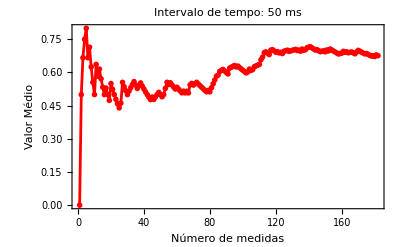
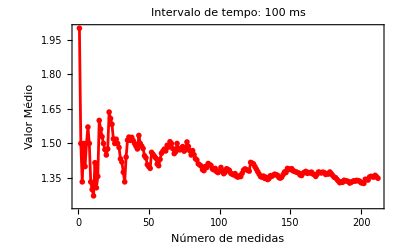
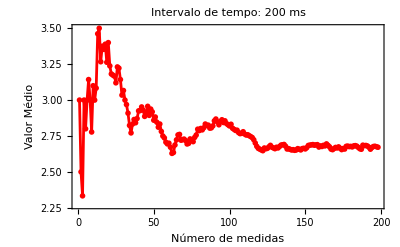
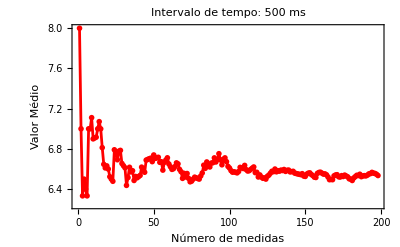
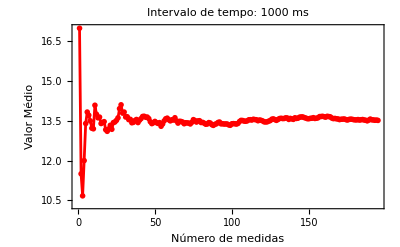
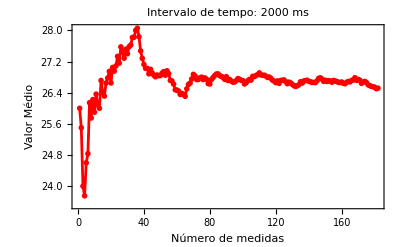
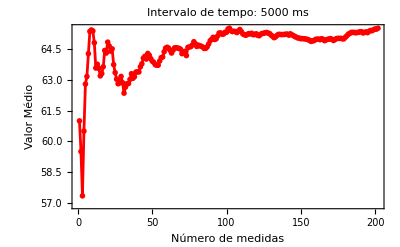
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | Spacer[]

```mathematica
Grid[{{Show[grafmed50G2,PlotLabel->"Intervalo de tempo: 50 ms",ImageSize->400],Show[grafmed100G2,PlotLabel->"Intervalo de tempo: 100 ms",ImageSize->400]},{Show[grafmed200G2,PlotLabel->"Intervalo de tempo: 200 ms",ImageSize->400],Show[grafmed500G2,PlotLabel->"Intervalo de tempo: 500 ms",ImageSize->400]},{Show[grafmed1000G2,PlotLabel->"Intervalo de tempo: 1000 ms",ImageSize->400],Show[grafmed2000G2,PlotLabel->"Intervalo de tempo: 2000 ms",ImageSize->400]},{Show[grafmed5000G2,PlotLabel->"Intervalo de tempo: 5000 ms",ImageSize->400],Spacer[]}},Alignment->Center,Spacings->{2,2}]
```

Gráficos com a variação do erro da média com o número de medidas

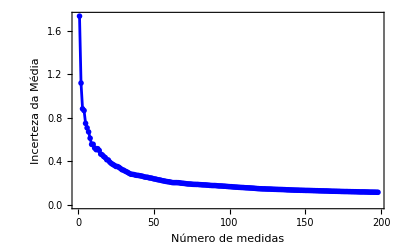

```mathematica
n50ms=Length[dados50G2];
media50ms=Mean[dados50G2];
desvioPadrao50ms=StandardDeviation[dados50G2];
x = N[Accumulate[dados200G2]/Range[n200G2]];
y = N[Sqrt[Accumulate[dados200G2]/Range[n200G2]^2]];
y== N[Sqrt[x]/ Range[n200G2]];
grafIncertezaMed200ms=ListPlot[y,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,PlotStyle->Blue,PlotLegends->None,FrameLabel->{"Número de medidas","Incerteza da Média","Variação da Incerteza da Média com o Número de Medidas","Intervalo de tempo: 100 ms"}]
```

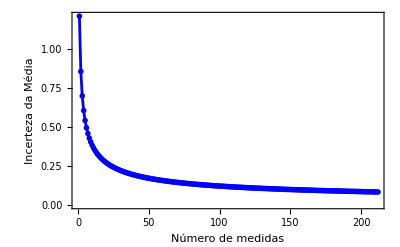

```mathematica
n100ms=Length[dados100G2];
media100ms=Mean[dados100G2];
desvioPadrao100ms=StandardDeviation[dados100G2];
incertezaMed100ms=desvioPadrao100ms/Sqrt[Range[n100ms]];

incertezaMed100msParcial=incertezaMed100ms;

grafIncertezaMed100ms=ListPlot[incertezaMed100msParcial,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,PlotStyle->Blue,PlotLegends->None,FrameLabel->{"Número de medidas","Incerteza da Média","Variação da Incerteza da Média com o Número de Medidas","Intervalo de tempo: 100 ms"}]
```

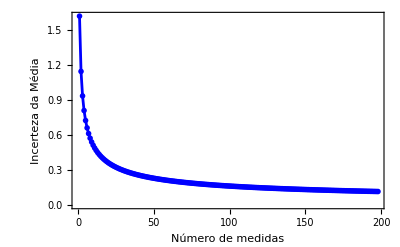

```mathematica
n200ms=Length[dados200G2];
media200ms=Mean[dados200G2];
desvioPadrao200ms=StandardDeviation[dados200G2];
incertezaMed200ms=desvioPadrao200ms/Sqrt[Range[n200ms]];

incertezaMed200msParcial=incertezaMed200ms;

grafIncertezaMed200ms=ListPlot[incertezaMed200msParcial,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,PlotStyle->Blue,PlotLegends->None,FrameLabel->{"Número de medidas","Incerteza da Média","Variação da Incerteza da Média com o Número de Medidas","Intervalo de tempo: 200 ms"}]
```

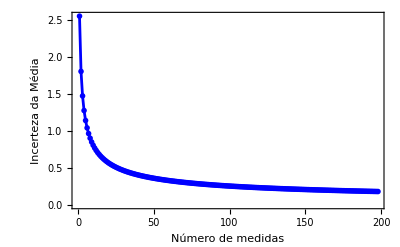

```mathematica
n500ms=Length[dados500G2];
media500ms=Mean[dados500G2];
desvioPadrao500ms=StandardDeviation[dados500G2];
incertezaMed500ms=desvioPadrao500ms/Sqrt[Range[n500ms]];

incertezaMed500msParcial=incertezaMed500ms;

grafIncertezaMed500ms=ListPlot[incertezaMed500msParcial,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,PlotStyle->Blue,PlotLegends->None,FrameLabel->{"Número de medidas","Incerteza da Média","Variação da Incerteza da Média com o Número de Medidas","Intervalo de tempo: 500 ms"}]
```

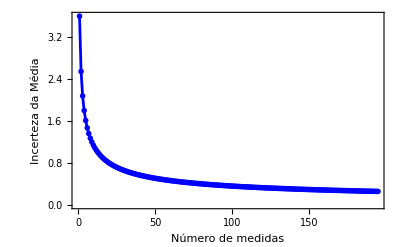

```mathematica
n1000ms=Length[dados1000G2];
media2000ms=Mean[dados2000G2];
desvioPadrao1000ms=StandardDeviation[dados1000G2];
incertezaMed1000ms=desvioPadrao1000ms/Sqrt[Range[n1000ms]];

incertezaMed1000msParcial=incertezaMed1000ms;

grafIncertezaMed1000ms=ListPlot[incertezaMed1000msParcial,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,PlotStyle->Blue,PlotLegends->None,FrameLabel->{"Número de medidas","Incerteza da Média","Variação da Incerteza da Média com o Número de Medidas","Intervalo de tempo: 1000 ms"}]
```

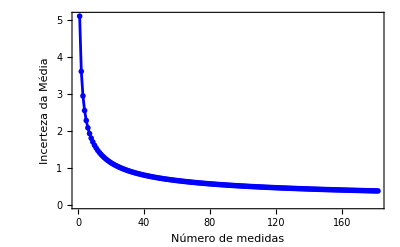

```mathematica
n2000ms=Length[dados2000G2];
media2000ms=Mean[dados2000G2];
desvioPadrao2000ms=StandardDeviation[dados2000G2];
incertezaMed2000ms=desvioPadrao2000ms/Sqrt[Range[n2000ms]];

incertezaMed2000msParcial=incertezaMed2000ms;

grafIncertezaMed2000ms=ListPlot[incertezaMed2000msParcial,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,PlotStyle->Blue,PlotLegends->None,FrameLabel->{"Número de medidas","Incerteza da Média","Variação da Incerteza da Média com o Número de Medidas","Intervalo de tempo: 2000 ms"}]
```

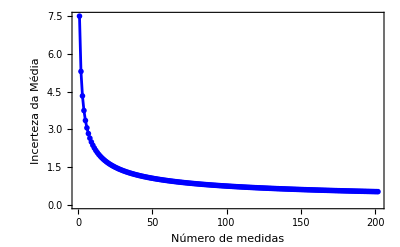

```mathematica
n5000ms=Length[dados5000G2];
media5000ms=Mean[dados5000G2];
desvioPadrao5000ms=StandardDeviation[dados5000G2];
incertezaMed5000ms=desvioPadrao5000ms/Sqrt[Range[n5000ms]];

incertezaMed5000msParcial=incertezaMed5000ms;

grafIncertezaMed5000ms=ListPlot[incertezaMed5000msParcial,Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,PlotStyle->Blue,PlotLegends->None,FrameLabel->{"Número de medidas","Incerteza da Média","Variação da Incerteza da Média com o Número de Medidas",None}]
```

Resultados BG

```mathematica
dadosBGcru = Import["G2_BG1000ms.txt", "Data"];
```

```mathematica
n1000G2 = Length[dados1000G2cru];
dados1000G2=ToExpression[Table[StringDrop[dados1000G2cru[[i,3]],3],{i,n1000G2}]];
```

```mathematica
nBGG2 = Length[dadosBGcru];
dadosBGG2=ToExpression[Table[StringDrop[dadosBGcru[[i,3]],3],{i,nBGG2}]];
resultado=dados1000G2-dadosBGG2;
```

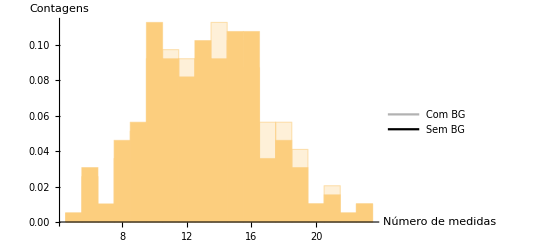

```mathematica
histogramaDados1000G2=Histogram[dados1000G2,Automatic,"PDF",ChartStyle->{Opacity[0.3]}];
histogramaResultado=Histogram[resultado,Automatic,"PDF",ChartStyle->{Opacity[1]}];

Legended[Show[histogramaDados1000G2,histogramaResultado,PlotRange->All,AxesLabel->{"Número de medidas","Contagens"}],Placed[LineLegend[{Opacity[0.3],Opacity[1]},{"Com BG","Sem BG"},LegendMarkerSize->{30,10}],Right]]
```

```mathematica
med100G2 = N[Total[resultado] / nBGG2]
```

13.1539

```mathematica
varBGG2 = N[Variance[resultado]]
```

13.0278

```mathematica
desvioPadraoBGG2=Sqrt[varBGG2];

(*Calculando a incerteza da média para diferentes intervalos de tempo*)
incertezaBGG2=desvioPadraoBGG2/Sqrt[nBGG2]
```

0.258474

```mathematica
decaimentoBGG2 = med100G2/1
incdecayBG = incertezaBGG2/1
```

13.1538

0.258474

```mathematica
Quit[]
```